### BioRxive statistics

#### Papers I’ve uploaded

```mathematica
websites={"http://biorxiv.org/content/early/2016/11/14/087171.article-metrics","http://biorxiv.org/content/early/2016/05/24/055020.article-metrics","http://biorxiv.org/content/early/2016/10/25/083089.article-metrics","http://biorxiv.org/content/early/2016/02/17/039909.article-metrics","http://biorxiv.org/content/early/2016/06/07/057570.article-metrics","http://biorxiv.org/content/early/2017/01/09/099127.article-metrics"};
```

#### Extract metrics

```mathematica
totalAbstract=0;
totalPDF=0;
For[i=1,i≤Length[websites],i++,test=Flatten[Import[websites[[i]],"FullData"]];
start=Position[test,"PDF"][[1,1]];
end=Quiet[Position[test,x_/;Not[StringFreeQ[x,"Posted"]]]][[1,1]];
abstractCount=Total[ToExpression/@test[[start+1;;end-1]][[2;;All;;3]]];
PDFCount=Total[ToExpression/@test[[start+1;;end-1]][[3;;All;;3]]];
totalAbstract=totalAbstract+abstractCount;
totalPDF=totalPDF+PDFCount;]
```

#### Plot the results

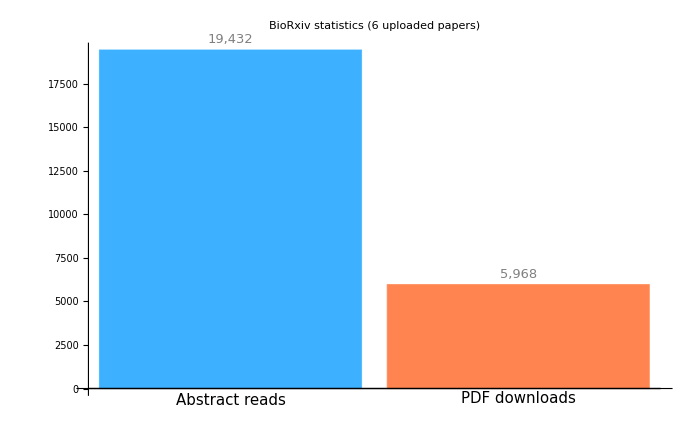

```mathematica
font=15;
out=BarChart[{Labeled[totalAbstract,Style["Abstract reads",Black,FontSize->font],Below],Labeled[totalPDF,Style["PDF downloads",Black,FontSize->font]]},ChartStyle->96,ChartLabels->Placed[Style[ToString[NumberForm[#,DigitBlock->3]],Gray,FontSize->font-2]&/@{totalAbstract,totalPDF},Above],PlotLabel->Style["BioRxiv statistics\n ("<>ToString[Length[websites]]<>" uploaded papers)",Black,FontSize->font+2],ImageSize->700]
```

#### Save the results

```mathematica
Export["/home/dkoslicki/Dropbox/AllPapers/BioRxivStats.png",out,ImageResolution->400,ImageSize->450,Antialiasing->True]
```

/home/dkoslicki/Dropbox/AllPapers/BioRxivStats.png

```mathematica
Export["/home/dkoslicki/Dropbox/AllPapers/BioRxivStats.gif",out,ImageSize->{300,300},ImageResolution->800]
```

/home/dkoslicki/Dropbox/AllPapers/BioRxivStats.gif

#### To get the source code as text, first copy as text, paste in drupal, turn off rich text, copy, paste in mathematica, say yes to prompt, replace special characters and delete the backslashes, evaluate, copy, paste in drupal, save.

```mathematica
StringReplace["<p><em>websites={\"http://biorxiv.org/content/early/2016/11/14/087171.article-metrics\",\"http://biorxiv.org/content/early/2016/05/24/055020.article-metrics\",\"http://biorxiv.org/content/early/2016/10/25/083089.article-metrics\",\"http://biorxiv.org/content/early/2016/02/17/039909.article-metrics\",\"http://biorxiv.org/content/early/2016/06/07/057570.article-metrics\",\"http://biorxiv.org/content/early/2017/01/09/099127.article-metrics\"};</em></p>
<p><em>totalAbstract=0;<br>
\ttotalPDF=0;</em></p>
<p><em>For&amp;#91;i=1,i&lt;=Length&amp;#91;websites&amp;#93;,i++,test=Flatten&amp;#91;Import&amp;#91;websites&amp;#91;&amp;#91;i&amp;#93;&amp;#93;,\"FullData\"&amp;#93;&amp;#93;;</em></p>
<p><em>start=Position&amp;#91;test,\"PDF\"&amp;#93;&amp;#91;&amp;#91;1,1&amp;#93;&amp;#93;;<br>
\tend=Quiet&amp;#91;Position&amp;#91;test,x_/;Not&amp;#91;StringFreeQ&amp;#91;x,\"Posted\"&amp;#93;&amp;#93;&amp;#93;&amp;#93;&amp;#91;&amp;#91;1,1&amp;#93;&amp;#93;;<br>
\tabstractCount=Total&amp;#91;ToExpression/@test&amp;#91;&amp;#91;start+1;;end-1&amp;#93;&amp;#93;&amp;#91;&amp;#91;2;;All;;3&amp;#93;&amp;#93;&amp;#93;;<br>
\tPDFCount=Total&amp;#91;ToExpression/@test&amp;#91;&amp;#91;start+1;;end-1&amp;#93;&amp;#93;&amp;#91;&amp;#91;3;;All;;3&amp;#93;&amp;#93;&amp;#93;;<br>
\ttotalAbstract=totalAbstract+abstractCount;<br>
\ttotalPDF=totalPDF+PDFCount;&amp;#93;</em></p>
<p><em>font=15;<br>
\tout=BarChart&amp;#91;{Labeled&amp;#91;totalAbstract,Style&amp;#91;\"Abstract reads\",Black,FontSize-&gt;font&amp;#93;,Below&amp;#93;,Labeled&amp;#91;totalPDF,Style&amp;#91;\"PDF downloads\",Black,FontSize-&gt;font&amp;#93;&amp;#93;},ChartStyle-&gt;96,ChartLabels-&gt;Placed&amp;#91;Style&amp;#91;ToString&amp;#91;NumberForm&amp;#91;#,DigitBlock-&gt;3&amp;#93;&amp;#93;,Gray,FontSize-&gt;font-2&amp;#93;&amp;/@{totalAbstract,totalPDF},Above&amp;#93;,PlotLabel-&gt;Style&amp;#91;\"BioRxiv statisticsn (\"&lt;&gt;ToString&amp;#91;Length&amp;#91;websites&amp;#93;&amp;#93;&lt;&gt;\" uploaded papers)\",Black,FontSize-&gt;font+2&amp;#93;,ImageSize-&gt;700&amp;#93;</em></p>
<p><br>
\t<em>Export&amp;#91;\"~/BioRxivStats.gif\",out,ImageSize-&gt;{300,300},ImageResolution-&gt;800&amp;#93;</em></p>
",{"&amp;"->"&","\\"->""}]
```

<p><em>websites={"http://biorxiv.org/content/early/2016/11/14/087171.article-metrics","http://biorxiv.org/content/early/2016/05/24/055020.article-metrics","http://biorxiv.org/content/early/2016/10/25/083089.article-metrics","http://biorxiv.org/content/early/2016/02/17/039909.article-metrics","http://biorxiv.org/content/early/2016/06/07/057570.article-metrics","http://biorxiv.org/content/early/2017/01/09/099127.article-metrics"};</em></p>
<p><em>totalAbstract=0;<br>
	totalPDF=0;</em></p>
<p><em>For&#91;i=1,i&lt;=Length&#91;websites&#93;,i++,test=Flatten&#91;Import&#91;websites&#91;&#91;i&#93;&#93;,"FullData"&#93;&#93;;</em></p>
<p><em>start=Position&#91;test,"PDF"&#93;&#91;&#91;1,1&#93;&#93;;<br>
	end=Quiet&#91;Position&#91;test,x_/;Not&#91;StringFreeQ&#91;x,"Posted"&#93;&#93;&#93;&#93;&#91;&#91;1,1&#93;&#93;;<br>
	abstractCount=Total&#91;ToExpression/@test&#91;&#91;start+1;;end-1&#93;&#93;&#91;&#91;2;;All;;3&#93;&#93;&#93;;<br>
	PDFCount=Total&#91;ToExpression/@test&#91;&#91;start+1;;end-1&#93;&#93;&#91;&#91;3;;All;;3&#93;&#93;&#93;;<br>
	totalAbstract=totalAbstract+abstractCount;<br>
	totalPDF=totalPDF+PDFCount;&#93;</em></p>
<p><em>font=15;<br>
	out=BarChart&#91;{Labeled&#91;totalAbstract,Style&#91;"Abstract reads",Black,FontSize-&gt;font&#93;,Below&#93;,Labeled&#91;totalPDF,Style&#91;"PDF downloads",Black,FontSize-&gt;font&#93;&#93;},ChartStyle-&gt;96,ChartLabels-&gt;Placed&#91;Style&#91;ToString&#91;NumberForm&#91;#,DigitBlock-&gt;3&#93;&#93;,Gray,FontSize-&gt;font-2&#93;&/@{totalAbstract,totalPDF},Above&#93;,PlotLabel-&gt;Style&#91;"BioRxiv statisticsn ("&lt;&gt;ToString&#91;Length&#91;websites&#93;&#93;&lt;&gt;" uploaded papers)",Black,FontSize-&gt;font+2&#93;,ImageSize-&gt;700&#93;</em></p>
<p><br>
	<em>Export&#91;"~/BioRxivStats.gif",out,ImageSize-&gt;{300,300},ImageResolution-&gt;800&#93;</em></p>